```mathematica
array1=Import["C:\Users\Mr\Workspace\MPLAB_projects\dspic33_FFT_DSPLib.X\adc_samples.mch","Text"];
```

```mathematica
array2=StringSplit[array1]
```

{5270,7A10,7FF0,7FF0,7FF0,7FF0,7320,6D50,64C0,5FD0,5230,4CB0,45B0,42D0,36F0,31A0,2F70,3C20,5C50,7FF0,7FF0,7FF0,7FF0,7FF0,6FA0,6C50,6270,5B00,4F90,4B90,42E0,3ED0,3450,3050,2D80,42C0,64C0,7FF0,7FF0,7FF0,7FF0,7F80,7020,6A90,6090,58D0,4AD0,49C0,4100,3AD0,2F80,2EC0,2EB0,4AA0,6C50,7FF0,7FF0,7FF0,7FF0,7CE0,7280,6910,5F70,57B0,4C10,4760,3EF0,39E0,2DD0,2CC0,31A0,5120,73C0,7FF0,7FF0,7FF0,7FF0,7870,6DE0,6A10,5CC0,5570,5000,4860,3E90,3830,2E70,2D20,3850,5A80,7A90,7FF0,7FF0,7FF0,7D30,7520,6B40,6660,5850,5340,4B10,4850,3C30,36B0,3170,2E40,3E20,6450,7FF0,7FF0,7FF0,7FF0,7990,7340,6900,6130,5570,5190,48D0,44B0,3A10,35A0,2E80,31D0,45C0,6E20,7FF0,7FF0,7FF0,7FF0,7980,72E0,68B0,5FD0,5120,4FD0,4770,3FA0,34F0,3420,2DC0,34B0,52F0,7740,7FF0,7FF0,7FF0,7FF0,7B30,70B0,6550,5E30,5300,4E80,4680,66B0,6030,59A0,50E0,4720,4060,3740,3380,2B70,3320,4B30,7880,7FF0,7FF0,7FF0,7FF0,78B0,7110,6530,5EB0,5550,5070,45C0,4010,3A40,32A0,2BA0,3930,57D0,7FF0,7FF0,7FF0,7FF0,7FF0,7570,6B00,5EB0,5B00,5290,4DE0,40B0,3CF0,3640,33A0,2C50,4020,6840,7FF0,7FF0,7FF0,7FF0,7FF0,7370,69C0,5AA0,58E0,50F0,4840,3CA0,3BE0,33F0,3050,2CD0,47B0,6E00,7FF0,7FF0,7FF0,7FF0,7E70,71B0,6820,5CE0,5800,4E60,4780,3B40,3A60,31C0,2C20,2E60,4EF0,75E0,7FF0,7FF0,7FF0,7FF0,7D20,6E50,66A0,6160,5970,4D50,4610,3D20,3A20,3060,2C80,31D0,5A00,7D70}

```mathematica
(*array2={"8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","7FF0","7FF0","7FF0","7FF0","7FF0","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","7FF0","7FF0","7FF0","7FF0","7FF0","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","7FF0","7FF0","7FF0","7FF0","7FF0","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","7FF0","7FF0","7FF0","7FF0","7FF0","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","7FF0","7FF0","7FF0","7FF0","7FF0","7FF0","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","7FF0","7FF0","7FF0","7FF0","7FF0","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","7FF0","7FF0","7FF0","7FF0","7FF0","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","7FF0","7FF0","7FF0","7FF0","7FF0","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","7FF0","7FF0","7FF0","7FF0","7FF0","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","7FF0","7FF0","7FF0","7FF0","7FF0","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","7FF0","7FF0","7FF0","7FF0","7FF0","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","7FF0","7FF0","7FF0","7FF0","7FF0","7FF0","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","8000","7FF0","7FF0","7FF0","7FF0","7FF0","8000","8000","8000","8000","8000","8000","8000"};*)
```

```mathematica
array3=FromDigits[#,16]&/@ array2;
```

```mathematica
Length[array3]

For[i=1,i<=Length[array3],i++,
If[array3[[i]]>32767,array3[[i]]=0,array3[[i]]=array3[[i]]/32767]
(*array3[[i]]=array3[[i]]/32767*)
]
```

256

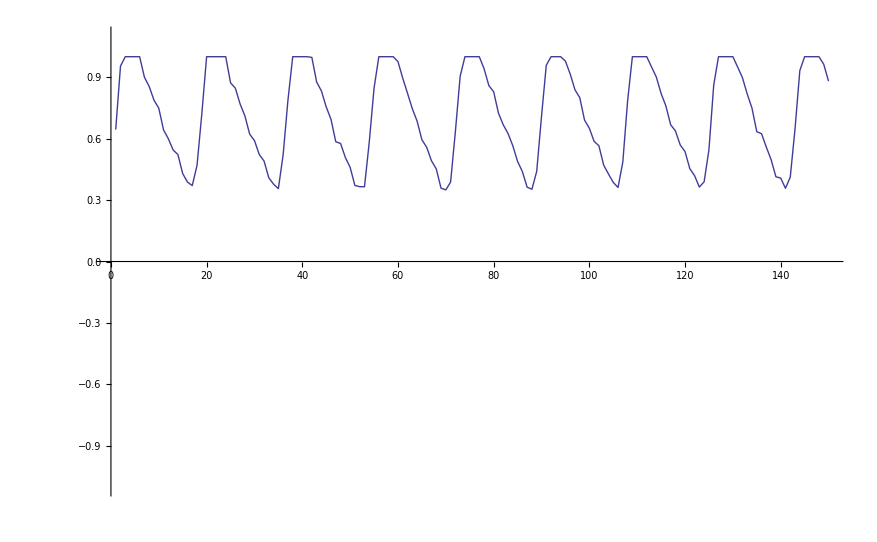

```mathematica
ListLinePlot[array3[[1;;150]],PlotRange->{-1.1,1.1}]
```

```mathematica
(*array3=Join[array3,ConstantArray[0,256]];*)
```

```mathematica
fftresults=Abs[Fourier[array3]];
```

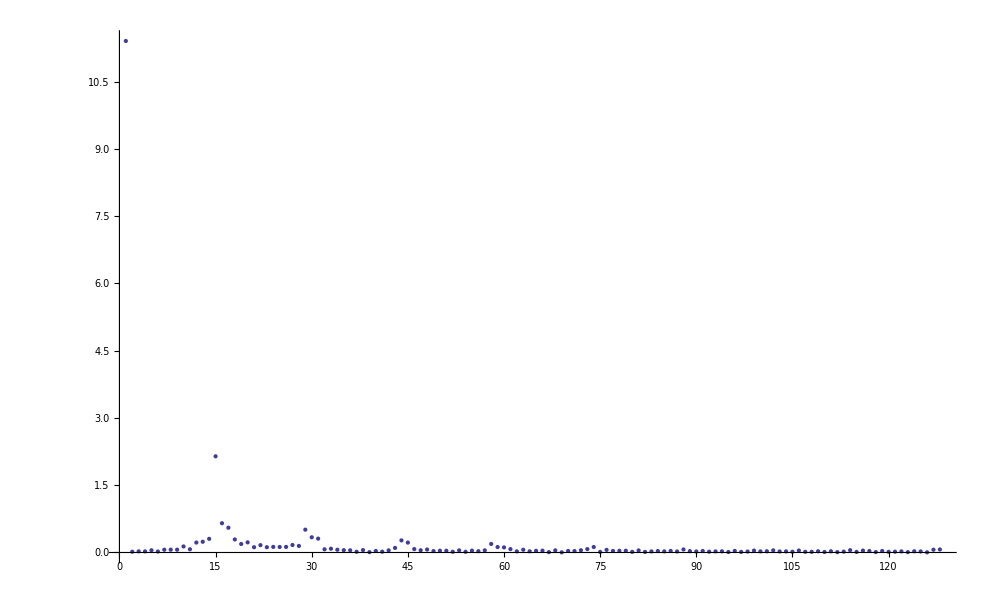

```mathematica
ListPlot[fftresults[[1;;128]],PlotRange->Full]
```